{-1/r[t]^3+1/r[t]^2+r''[t]==0,r[t]^2 θ'[t]==1}

{r[0]==2+√2,r'[0]==0,θ[0]==0}

{{r[t]→InterpolatingFunction[…][t],r'[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],θ'[t]→InterpolatingFunction[…][t]}}

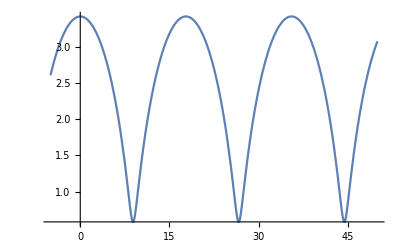

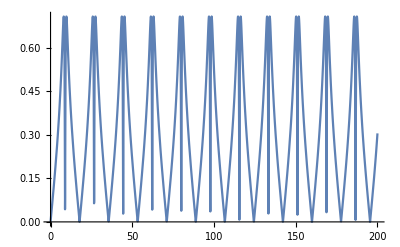

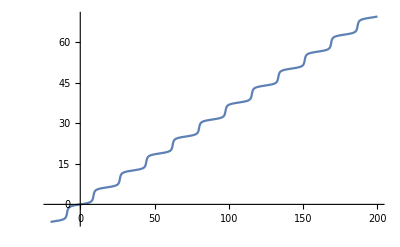

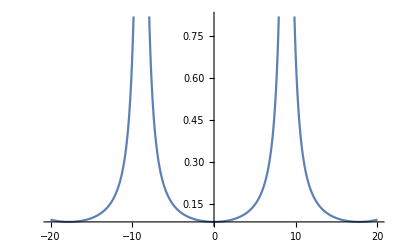

-Graphics3D-

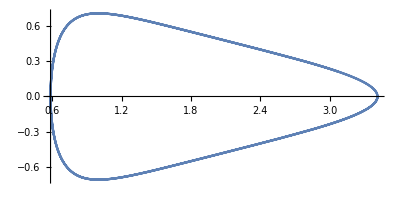

-Graphics3D-

```mathematica
[for  every plot, I have used the initial condition from calculation in written copy. For every orbit, the plots are respectively of  r(t), r'(t), θ(t), θ'(t), parametric[r,r',Subscript[p, r]],parametric[r,Subscript[p, r]], parametric[r,θ,Subscript[p, r]]]









For ellipse:

s={r''[t ]-1/(1*(r[t])^3)+1/(r[t])^2==0,(r[t])^2*θ'[t]==1}
ics= {r[0]==2+√2,r'[0]==0,θ[0]==0}
sol=NDSolve[{s,ics},{r[t],r'[t],θ[t],θ'[t]},{t,-200,200}]
Plot[Evaluate[r[t]/.sol],{t,-5,50}]
Plot[Evaluate[Abs[r'[t]]/.sol],{t,0,200}]
Plot[Evaluate[θ[t]/.sol],{t,-20,200}]
Plot[Evaluate[θ'[t]/.sol],{t,-20,20}]
ParametricPlot3D[{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,50}]

ParametricPlot[{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,50}]

ParametricPlot3D[{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,50}]
```

```mathematica
For Parabola:
```

{-1/r[t]^3+1/r[t]^2+r''[t]==0,r[t]^2 θ'[t]==1}

{r[0]==0.5,r'[0]==0,θ[0]==0}

{{r[t]→InterpolatingFunction[…][t],r'[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],θ'[t]→InterpolatingFunction[…][t]}}

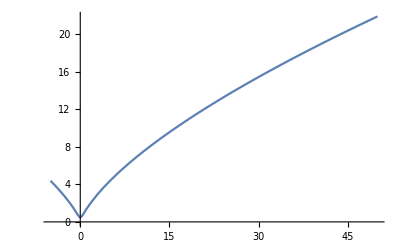

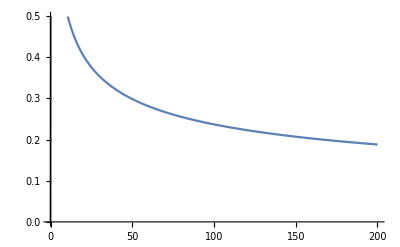

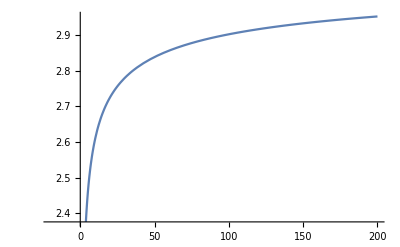

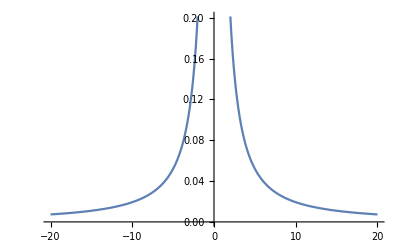

-Graphics3D-

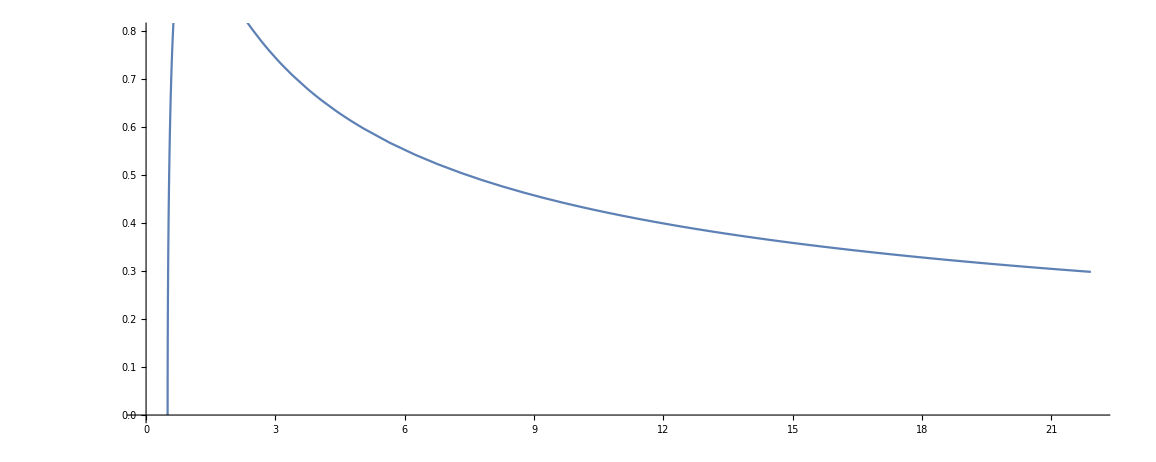

-Graphics3D-

```mathematica
s={r''[t ]-1/(1*(r[t])^3)+1/(r[t])^2==0,(r[t])^2*θ'[t]==1}
ics= {r[0]==0.5,r'[0]==0,θ[0]==0}
sol=NDSolve[{s,ics},{r[t],r'[t],θ[t],θ'[t]},{t,-200,200}]
Plot[Evaluate[r[t]/.sol],{t,-5,50}]
Plot[Evaluate[Abs[r'[t]]/.sol],{t,0,200}]
Plot[Evaluate[θ[t]/.sol],{t,-20,200}]
Plot[Evaluate[θ'[t]/.sol],{t,-20,20}]
ParametricPlot3D[{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,50}]

ParametricPlot[{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,50}]

ParametricPlot3D[{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,50}]
```

```mathematica
For Circle:
```

{-1/r[t]^3+1/r[t]^2+r''[t]==0,r[t]^2 θ'[t]==1}

{r[0]==1,r'[0]==0,θ[0]==0}

{{r[t]→InterpolatingFunction[…][t],r'[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],θ'[t]→InterpolatingFunction[…][t]}}

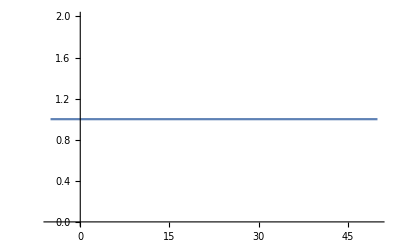

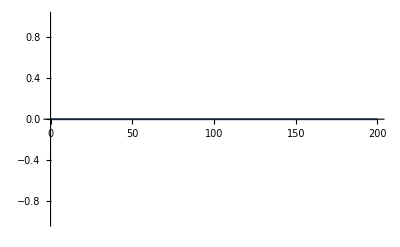

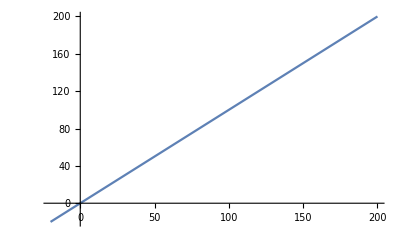

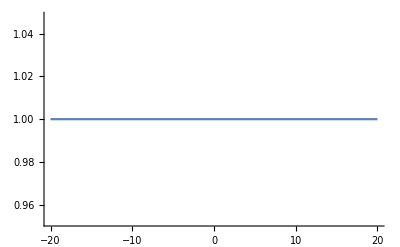

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
s={r''[t ]-1/(1*(r[t])^3)+1/(r[t])^2==0,(r[t])^2*θ'[t]==1}
ics= {r[0]==1,r'[0]==0,θ[0]==0}
sol=NDSolve[{s,ics},{r[t],r'[t],θ[t],θ'[t]},{t,-200,200}]
Plot[Evaluate[r[t]/.sol],{t,-5,50}]
Plot[Evaluate[Abs[r'[t]]/.sol],{t,0,200}]
Plot[Evaluate[θ[t]/.sol],{t,-20,200}]
Plot[Evaluate[θ'[t]/.sol],{t,-20,20}]
ParametricPlot3D[{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,50}]

ParametricPlot3D[{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,50}]

ParametricPlot3D[{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,-2,50}]
```

```mathematica
For Hyperbola:
```

{-1/r[t]^3+1/r[t]^2+r''[t]==0,r[t]^2 θ'[t]==1}

{r[0]==1/2 (-1+√3),r'[0]==0,θ[0]==0}

{{r[t]→InterpolatingFunction[…][t],r'[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],θ'[t]→InterpolatingFunction[…][t]}}

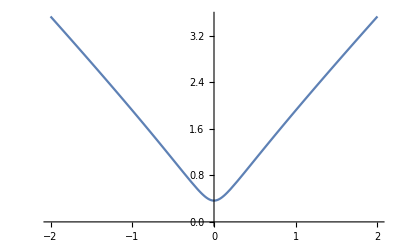

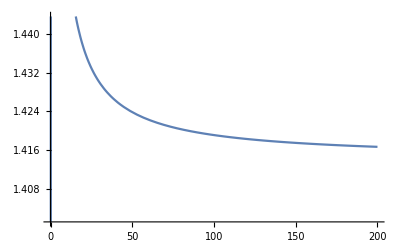

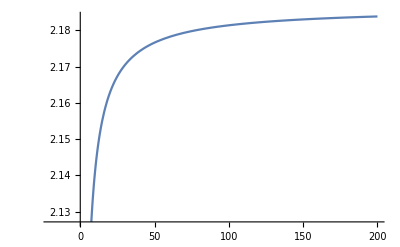

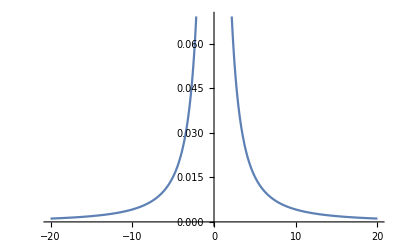

-Graphics3D-

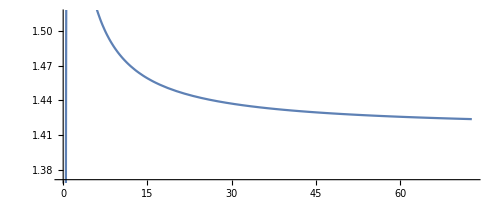

-Graphics3D-

```mathematica
s={r''[t ]-1/(1*(r[t])^3)+1/(r[t])^2==0,(r[t])^2*θ'[t]==1}
ics= {r[0]==(√3-1)/2,r'[0]==0,θ[0]==0}
sol=NDSolve[{s,ics},{r[t],r'[t],θ[t],θ'[t]},{t,-200,200}]
Plot[Evaluate[r[t]/.sol],{t,-2,2}]
Plot[Evaluate[Abs[r'[t]]/.sol],{t,0,200}]
Plot[Evaluate[θ[t]/.sol],{t,-20,200}]
Plot[Evaluate[θ'[t]/.sol],{t,-20,20}]
ParametricPlot3D[{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,50}]
ParametricPlot[{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,50}]
ParametricPlot3D[{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{t,0,50}]
```